```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
H[basissize_,g_]:= h0[basissize] - 3 x[basissize].x[basissize]/2 + g x[basissize].x[basissize].x[basissize].x[basissize]/4;
S[basissize_] := Transpose[Normalize /@ Eigenvectors[x[basissize]]];
fn[basissize_,g_,n_] := Sort[Eigenvalues[N[H[basissize,g]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
V[x_,g_] := g x^4 / 4 - x^2;
```

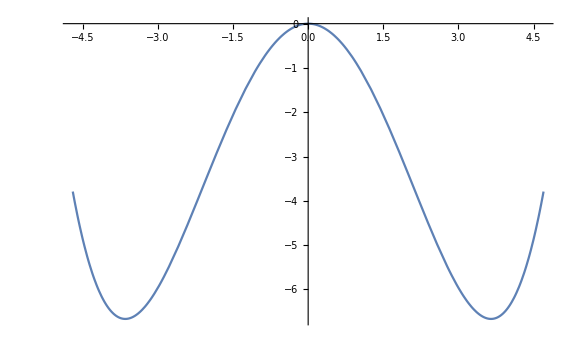

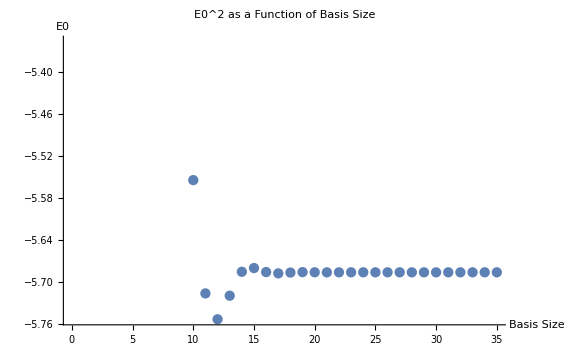

```mathematica
n = 0; g=0.15;
Plot[V[x,g],{x,-4.7,4.7}]
ListPlot[Table[{basissize,fn[basissize,g,n+1]},{basissize,5,35}],PlotLabel->"E0^2 as a Function of Basis Size",AxesLabel->{"Basis Size","E0"},ImageSize->Large]
```

-5.68592

{-0.0288743,0,-0.181677,0,-0.445793,0,-0.626932,0,-0.54513,0,-0.272936,0,-0.0406309,0,0.0327654,0}

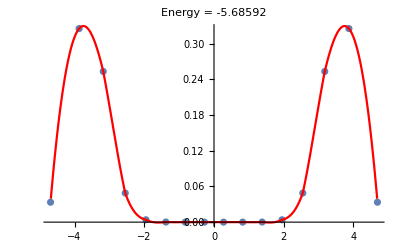

```mathematica
n = 0; bs = 16; g=.15;
{evals,evecs} = Eigensystem[N[H[bs,g]]];
{evals,evecs} = Transpose@SortBy[Transpose[{evals,evecs}],First];
e0 = Chop[evals[[n+1]]]
e0wf = Chop[evecs[[n+1]]]
energy[e0_,x_] := e0 /; e0 ≥ V[x];
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
fun = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2}]];
norm2 = NIntegrate[fun[x],{x,-4.68,4.68}];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2/norm2}],PlotRange->All];
p3 = Plot[fun[x]/norm2,{x,-4.68,4.68},PlotStyle->Hue[1],PlotRange->All];
Show[p2,p3,PlotLabel-> StringForm["Energy = ``",e0]]
```

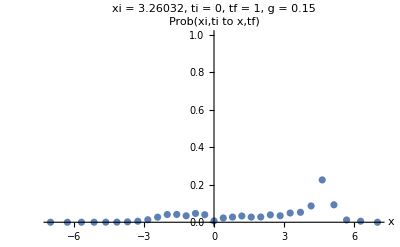

2.33583

```mathematica
Kmat[basissize_,g_,T_, t_]:= ConjugateTranspose[S[basissize]].MatrixExp[-I H [basissize,g](T-t)].S[basissize];
probabilities[basissize_,g_,T_, t_]:= Abs[Kmat[basissize,g,T, t]]^2;
bas = 31; T = 1; t = 0; xx = 15; g = 0.15;
ListPlot[Transpose[{xvals[bas],probabilities[bas,g,T,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``, g = ``",xvals[bas][[xx]],t,T,g],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4}{0,0.25}}]
animation = Table[ListPlot[Transpose[{xvals[bas],probabilities[bas,g,TF/20,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``, g = ``",xvals[bas][[xx]],t,N[TF/20],g],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4},{0,1}}],{TF,0,200}];
ListAnimate[animation,4]
(ConjugateTranspose[S[bas]].H [bas,g].S[bas])[[xx]][[xx]]
```

```mathematica
zbas = {{1,0},{0,1}};
flabels = Flatten[Table[{a-1,b-1,c-1,d-1}, {a,2},{b,2},{c,2},{d,2}]];
f3labels = Flatten[Table[{a-1,b-1,c-1}, {a,2},{b,2},{c,2}]];
labels = Table[{flabels[[4*k-3]],flabels[[4*k-2]],flabels[[4*k-1]],flabels[[4*k]]},{k,16}]
labels3 = Table[{f3labels[[3*k-2]],f3labels[[3*k-1]],f3labels[[3*k]]},{k,8}];
productbas = Table[Flatten[KroneckerProduct[zbas[[labels[[k]][[1]]+1]],zbas[[labels[[k]][[2]]+1]],zbas[[labels[[k]][[3]]+1]],zbas[[labels[[k]][[4]]+1]]]],{k,16}]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
specvec = {0,0,0,0,s1,0,c1,0,c2,0,s2,0,0,0,0,0};
proj = Table[e0wf.productbas[[k]],{k,16}]
```

{-0.0288743,0.,-0.181677,0.,-0.445793,0.,-0.626932,0.,-0.54513,0.,-0.272936,0.,-0.0406309,0.,0.0327654,0.}

```mathematica
contrib = Table[labels[[2*k-1]],{k,8}]
```

{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,1,1,0},{1,0,0,0},{1,0,1,0},{1,1,0,0},{1,1,1,0}}

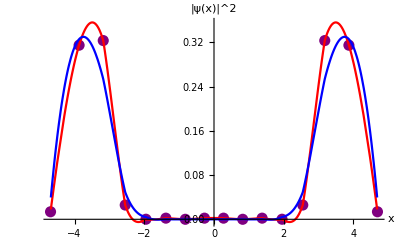

-5.54669

```mathematica
n = 0; bs = 16; g=.15;
e0wfvqe = {(-0.04099939891545329-0.026103447291551066I),(0.21313679655454007+0.1752391118557933I),(-0.07285315943496831-0.046286773797267776I),(0.3787964353885737+0.31083979758225366I),(-0.10287062868193866-0.060125371811478354I),(0.5384616680427448+0.4094250506003821I),(-0.07473222877384816-0.020387160269176852I),(0.4071587322351411+0.16617358063722182I),(-0.00023722155028192514+0.0025570002493355056I),(0.003091520494363937-0.01424703058764323I),(-0.0004169542620490583+0.004541268290022765I),(0.005466044013963623-0.02530591424073145I),(-0.0003428139016526298+0.006286087618520693I),(0.006245566184177571-0.03518961302054625I),(0.0008456587402181731+0.004004435426720886I),(-0.0020177210498607736-0.02314706009014029I),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};e0wfvqe = {0.03705883898610596,0.0,0.06091303842940861,0.0,0.4378757092637786,0.0,0.6615757809986048,0.0,0.5652550688562318,0.0,0.20536472479784493,0.0,-0.056698247725223506,0.0,-0.02441186353107207,0.0};
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
funvqe = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wfvqe]]^2}]];
norm2vqe= NIntegrate[funvqe[x],{x,-4.68,4.68}];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wfvqe]]^2/norm2vqe}],PlotRange->All,PlotStyle->{Purple,AbsolutePointSize[8]}];
p3 = Plot[funvqe[x]/norm2vqe,{x,-4.68,4.68},PlotStyle->Hue[1],PlotRange->All];
p4 = Plot[fun[x]/norm2,{x,-4.68,4.68},PlotStyle->Blue,PlotRange->All];
plot = Show[p2,p3,p4,PlotRange->All,AxesLabel->{"x","|ψ(x)|^2"}];
ShowLegend[plot,{{{Graphics[{Purple, Disk[{0,0},.05]}],"VQE Discrete"},{Graphics[{Thickness[.1],Red,Line[{{0,0},{2,0}}]}],"VQE Interpolation"},{Graphics[{Thickness[.1],Blue,Line[{{0,0},{2,0}}]}],"Matrix Interpolation"}},LegendPosition->{0.72,0.2},LegendSize->{0.6,0.4},LegendShadow->False}]
Chop[Conjugate[e0wfvqe].H[bs,g].e0wfvqe/Conjugate[e0wfvqe].e0wfvqe]
```

```mathematica
zbas = {{1,0},{0,1}};
flabels = Flatten[Table[{a-1,b-1,c-1,d-1,e-1}, {a,2},{b,2},{c,2},{d,2},{e,2}]];
labels = Table[{flabels[[5*k-4]],flabels[[5*k-3]],flabels[[5*k-2]],flabels[[5*k-1]],flabels[[5*k]]},{k,32}]
productbas = Table[Flatten[KroneckerProduct[zbas[[labels[[k]][[1]]+1]],zbas[[labels[[k]][[2]]+1]],zbas[[labels[[k]][[3]]+1]],zbas[[labels[[k]][[4]]+1]],zbas[[labels[[k]][[5]]+1]]]],{k,32}] 
contrib = Table[labels[[2*k-1]],{k,16}]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

{{0,0,0,0,0},{0,0,0,1,0},{0,0,1,0,0},{0,0,1,1,0},{0,1,0,0,0},{0,1,0,1,0},{0,1,1,0,0},{0,1,1,1,0},{1,0,0,0,0},{1,0,0,1,0},{1,0,1,0,0},{1,0,1,1,0},{1,1,0,0,0},{1,1,0,1,0},{1,1,1,0,0},{1,1,1,1,0}}

```mathematica
proj = Table[e0wf.productbas[[k]],{k,32}]
```

{-0.0840298,0.,-0.377367,0.,-0.648817,0.,-0.593613,0.,-0.274504,0.,-0.0176682,0.,0.0380238,0.,0.00613814,0.,-0.00653816,0.,-0.000556168,0.,0.00129346,0.,-0.000150474,0.,-0.000219157,0.,0.0000928046,0.,0.0000186568,0.,-0.0000290219,0.}

```mathematica
H[bs,g] // MatrixForm
```

(-0.2125 | 0. | -0.954594 | 0. | 0.0612372 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5625 | 0. | -1.53093 | 0. | 0.136931 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.954594 | 0. | -0.7625 | 0. | -1.99186 | 0. | 0.237171 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -1.53093 | 0. | -0.8125 | 0. | -2.34787 | 0. | 0.362284 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0612372 | 0. | -1.99186 | 0. | -0.7125 | 0. | -2.60168 | 0. | 0.512348 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.136931 | 0. | -2.34787 | 0. | -0.4625 | 0. | -2.75431 | 0. | 0.687386 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.237171 | 0. | -2.60168 | 0. | -0.0625 | 0. | -2.80624 | 0. | 0.887412 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.362284 | 0. | -2.75431 | 0. | 0.4875 | 0. | -2.75772 | 0. | 1.11243 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.512348 | 0. | -2.80624 | 0. | 1.1875 | 0. | -2.60888 | 0. | 1.36244 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.687386 | 0. | -2.75772 | 0. | 2.0375 | 0. | -2.35982 | 0. | 1.63745 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.887412 | 0. | -2.60888 | 0. | 3.0375 | 0. | -2.0106 | 0. | 1.93746 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.11243 | 0. | -2.35982 | 0. | 4.1875 | 0. | -1.56125 | 0. | 2.26247 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.36244 | 0. | -2.0106 | 0. | 5.4875 | 0. | -1.01181 | 0. | 2.61247 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.63745 | 0. | -1.56125 | 0. | 6.9375 | 0. | -0.362284 | 0. | 2.98747 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.93746 | 0. | -1.01181 | 0. | 8.5375 | 0. | 0.387298 | 0. | 3.38748 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.26247 | 0. | -0.362284 | 0. | 10.2875 | 0. | 1.23693 | 0. | 3.81248 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.61247 | 0. | 0.387298 | 0. | 12.1875 | 0. | 2.18661 | 0. | 4.26248 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.98747 | 0. | 1.23693 | 0. | 14.2375 | 0. | 3.23632 | 0. | 4.73748 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.38748 | 0. | 2.18661 | 0. | 16.4375 | 0. | 4.38606 | 0. | 5.23749 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.81248 | 0. | 3.23632 | 0. | 18.7875 | 0. | 5.63582 | 0. | 5.76249 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.26248 | 0. | 4.38606 | 0. | 21.2875 | 0. | 6.98561 | 0. | 6.31249 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4.73748 | 0. | 5.63582 | 0. | 23.9375 | 0. | 8.43542 | 0. | 6.88749 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.23749 | 0. | 6.98561 | 0. | 26.7375 | 0. | 9.98524 | 0. | 7.48749 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 5.76249 | 0. | 8.43542 | 0. | 29.6875 | 0. | 11.6351 | 0. | 8.11249 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.31249 | 0. | 9.98524 | 0. | 32.7875 | 0. | 13.3849 | 0. | 8.76249 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 6.88749 | 0. | 11.6351 | 0. | 36.0375 | 0. | 15.2348 | 0. | 9.43749 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 7.48749 | 0. | 13.3849 | 0. | 39.4375 | 0. | 17.1847 | 0. | 10.1375 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.11249 | 0. | 15.2348 | 0. | 42.9875 | 0. | 19.2345 | 0. | 10.8625
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 8.76249 | 0. | 17.1847 | 0. | 46.6875 | 0. | 21.3844 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 9.43749 | 0. | 19.2345 | 0. | 50.5375 | 0. | 11.436
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10.1375 | 0. | 21.3844 | 0. | 42.1375 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 10.8625 | 0. | 11.436 | 0. | 31.8875)

```mathematica
u3[theta_,phi_,lambda_]:={{Cos[theta/2], -Exp[ I lambda]Sin[theta/2]},{Exp[I phi]Sin[theta/2], Exp[I lambda]Exp[I phi]Cos[theta/2]}};
v1  = {1,0};
v2 = {1,0};
v3  = {1,0};
v4 = {1,0};
v5 = {1,0};
Flatten[KroneckerProduct[v1,u3[theta3,0,0].u3[Pi,0,0].v2,u3[theta4,0,0].u3[theta2,0,0].u3[Pi,0,0].v3,u3[theta1,0,0].u3[Pi,0,0].v4,v5]] // MatrixForm
```

(Sin[theta1/2] Sin[theta3/2] (-Cos[theta4/2] Sin[theta2/2]-Cos[theta2/2] Sin[theta4/2])
0
-Cos[theta1/2] Sin[theta3/2] (-Cos[theta4/2] Sin[theta2/2]-Cos[theta2/2] Sin[theta4/2])
0
Sin[theta1/2] Sin[theta3/2] (Cos[theta2/2] Cos[theta4/2]-Sin[theta2/2] Sin[theta4/2])
0
-Cos[theta1/2] Sin[theta3/2] (Cos[theta2/2] Cos[theta4/2]-Sin[theta2/2] Sin[theta4/2])
0
-Cos[theta3/2] Sin[theta1/2] (-Cos[theta4/2] Sin[theta2/2]-Cos[theta2/2] Sin[theta4/2])
0
Cos[theta1/2] Cos[theta3/2] (-Cos[theta4/2] Sin[theta2/2]-Cos[theta2/2] Sin[theta4/2])
0
-Cos[theta3/2] Sin[theta1/2] (Cos[theta2/2] Cos[theta4/2]-Sin[theta2/2] Sin[theta4/2])
0
Cos[theta1/2] Cos[theta3/2] (Cos[theta2/2] Cos[theta4/2]-Sin[theta2/2] Sin[theta4/2])
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
N[{-0.02887431881332983,0,-0.18167674078833862,0,-0.44579279305307895,0,-0.6269317432444409,0,-0.5451298804749698,0,-0.2729362251224197,0,-0.04063091470514919,0,0.03276537415482568,0},5]
```

{-0.0288743,0,-0.181677,0,-0.445793,0,-0.626932,0,-0.54513,0,-0.272936,0,-0.0406309,0,0.0327654,0}

```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
G[basissize_,g_]:= p[basissize].p[basissize]/4 -  x[basissize].x[basissize]+ g x[basissize].x[basissize].x[basissize].x[basissize]/4;
H[basissize_,g_]:=  -KroneckerProduct[G[basissize,g],IdentityMatrix[basissize]] + KroneckerProduct[IdentityMatrix[basissize],G[basissize,g]];
S[basissize_] := KroneckerProduct[Transpose[Normalize /@ Eigenvectors[x[basissize]]],Transpose[Normalize /@ Eigenvectors[x[basissize]]]];
fn[basissize_,g_,n_] := Sort[Eigenvalues[N[H[basissize,g]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
V[x_,g_] := g x^4 / 4 - x^2;
```

0

-Graphics3D-

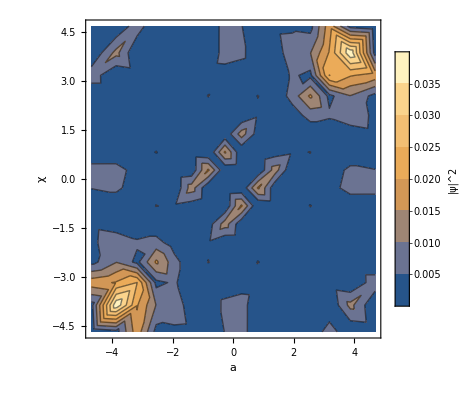

```mathematica
g = .15; bs = 16; n = 14;
Eigenvalues[G[bs,g]];
{evals,evecs}=Transpose@SortBy[Transpose[Chop[Eigensystem[H[bs,g].H[bs,g]]]],First];
x1vals[ basissize_] := Table[(ConjugateTranspose[S[basissize]].KroneckerProduct[x[basissize],IdentityMatrix[basissize]].S[basissize])[[m]][[m]],{m,basissize^2}];
x2vals[basissize_] := Table[(ConjugateTranspose[S[basissize]].KroneckerProduct[IdentityMatrix[basissize],x[basissize]].S[basissize])[[m]][[m]],{m,basissize^2}];
e0wf = {-0.02887431881332983,0,-0.18167674078833862,0,-0.44579279305307895,0,-0.6269317432444409,0,-0.5451298804749698,0,-0.2729362251224197,0,-0.04063091470514919,0,0.03276537415482568,0};
evals[[n]]
dewf = Flatten[KroneckerProduct[e0wf,e0wf]];
Chop[H[bs,g].H[bs,g].dewf];
ListPlot3D[Transpose[{x1vals[bs],x2vals[bs],toposbasis[bs,evecs[[n]]]^2}],PlotRange->All]
ListContourPlot[Transpose[{x1vals[bs],x2vals[bs],toposbasis[bs,evecs[[n]]]^2}],PlotRange->All,FrameLabel->{"a","χ"},PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"|ψ|^2"]]
```

-Graphics3D-

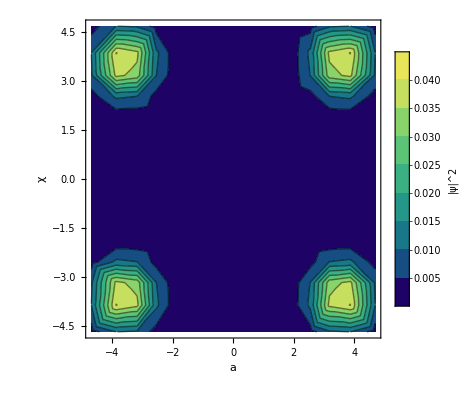

```mathematica
{vale,vece} = Transpose@SortBy[Transpose[Eigensystem[G[bs,g]]],First];
dewf = Flatten[KroneckerProduct[vece[[1]],vece[[1]]]];
ListPlot3D[Transpose[{x1vals[bs],x2vals[bs],toposbasis[bs,dewf]^2}],PlotRange->All]
ListContourPlot[Transpose[{x1vals[bs],x2vals[bs],toposbasis[bs,dewf]^2}],PlotRange->All,PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->"|ψ|^2"],FrameLabel->{"a","χ"},ColorFunction->"BlueGreenYellow"]
```